## Chirikov Standard Map F. I. Giasemis

### Credits

Eric W. Weisstein
March 18, 2006

This notebook downloaded from http://mathworld.wolfram.com/notebooks/DynamicalSystems/StandardMap.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/StandardMap.html.

©2006 Wolfram Research, Inc. except for portions noted otherwise

### Trying NestList

```mathematica
list =NestList[f,x,3]
Length[list]
```

{x,f[x],f[f[x]],f[f[f[x]]]}

4

```mathematica
NestList[(1+#)^2&,x,3]
```

{x,(1+x)^2,(1+(1+x)^2)^2,(1+(1+(1+x)^2)^2)^2}

```mathematica
NestList[(1+#)^2&,#,3]&[10 Random[Real]]
```

{7.57133,73.4677,5545.44,3.0763×10^7}

### Trying Random[Real]

```mathematica
Random[Real]
```

0.883972

```mathematica
t=Table[Random[Real],{2}]
```

{0.260556,0.0181139}

```mathematica
t[[2]]
```

0.0181139

### Mathworld code implementation Random Initial conditions

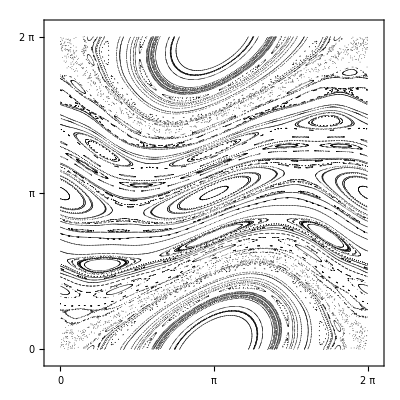
-Graphics-0.8

```mathematica
k=0.8;
(* [[1]], [[2]]: θ, Ι. *)
(* The two random numbers between 0 and 2π are the initial conditions. *)
iters=500; (* Iterations. *)
cnt=100;
T=Table[NestList[Mod[{#[[1]]+#[[2]]+k Sin[#[[1]]],#[[2]]+k Sin[#[[1]]]},2Pi]&,#,iters]&[Table[2π Random[Real],{2}]],{cnt}];
T=Flatten[T,1];
Labeled[ListPlot[T,PlotStyle->{Black,PointSize[0.001]},AspectRatio->Automatic,FrameTicks->{{0,Pi,2Pi},{0,Pi,2Pi}},PlotRange->{{-.2,2Pi+.2},{-.2,2Pi+.2}},Frame->True],Style[k,"Graphics"]]
```

### Modification of the Mathworld code Grid of initial conditions

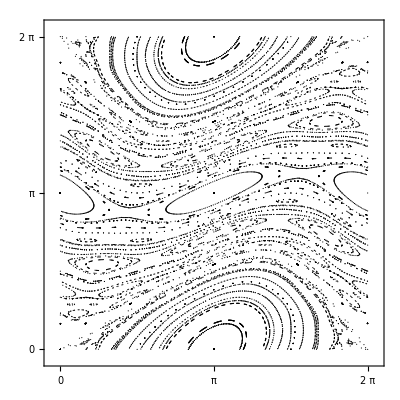
-Graphics-0.8

```mathematica
k=0.8;
(* [[1]], [[2]]: θ, Ι. *)
(* The two random numbers between 0 and 2π are the initial conditions. *)
iters=100; (* Iterations. *)
steps=12;
T={};
For[i=0,i≤2Pi,i=i+2Pi/steps,
For[j=0,j≤2Pi,j=j+2Pi/steps,
AppendTo[T,NestList[Mod[{#[[1]]+#[[2]]+k Sin[#[[1]]],#[[2]]+k Sin[#[[1]]]},2Pi]&,#,iters]&[{i,j}]]
]]
T=Flatten[T,1];
Labeled[ListPlot[T,PlotStyle->{Black,PointSize[0.002]},AspectRatio->Automatic,FrameTicks->{{0,Pi,2Pi},{0,Pi,2Pi}},Frame->True, PlotRange->{{-.2,2Pi+.2},{-.2,2Pi+.2}}],Style[k,"Graphics"]]
```

### Interactive version: variable parameter k

```mathematica
iters=100; 
cnt=50;
Manipulate[Labeled[ListPlot[Flatten[Table[NestList[Mod[{#[[1]]+#[[2]]+k Sin[#[[1]]],#[[2]]+k Sin[#[[1]]]},2Pi]&,#,iters]&[Table[2π Random[Real],{2}]],{cnt}],1],PlotStyle->{Black,PointSize[0.001]},AspectRatio->Automatic,FrameTicks->{{0,Pi,2Pi},{0,Pi,2Pi}},Frame->True, PlotRange->{{-.2,2Pi+.2},{-.2,2Pi+.2}}],Style[k,"Graphics"]],{k,0,7,0.5}]
```

### Visible initial conditions

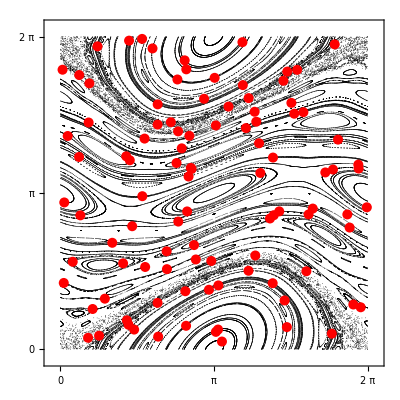
-Graphics-0.8

```mathematica
k=.8;
(* [[1]], [[2]]: θ, Ι. *)
(* The two random numbers between 0 and 2π are the initial conditions. *)
iters=1000; (* Iterations. *)
cnt=100;
T={};
initlist={};
For[i=1,i≤cnt,i++,
initcond=Table[2π Random[Real],{2}];
initlist=AppendTo[initlist,initcond];
T=AppendTo[T,NestList[Mod[{#[[1]]+#[[2]]+k Sin[#[[1]]],#[[2]]+k Sin[#[[1]]]},2Pi]&,#,iters]&[initcond]];
]
T=Flatten[T,1];
Labeled[ListPlot[{T,initlist},PlotStyle->{{Black,PointSize[0.001]},{Red,PointSize[0.018]}},AspectRatio->Automatic,FrameTicks->{{0,Pi,2Pi},{0,Pi,2Pi}},PlotRange->{{-.2,2Pi+.2},{-.2,2Pi+.2}},Frame->True],Style[k,"Graphics"]]
```